## VA Formalism

## Constants

```mathematica
α=1/137.0359998;
GeV2nb = 0.389379*10^6;
Mp = 0.938272;

Jcob = N[2π];
Rad=π/180;
```

## Set Kinematics

```mathematica
y[QQ_,x_,k_]:= QQ/(2 Mp*k*x) ; 
g[QQ_,x_]:=(2Mp*x)/(√QQ);

transverse[v1_,v2_]:=v1[[2]]*v2[[2]]+v1[[3]]*v2[[3]];
ξ[QQ_,x_,t_]:=x*(1+t/(2 QQ))/(2-x+x*t/QQ);

tmin[QQ_,x_]:=-(QQ*(1-√(1+g[QQ,x]^2)+g[QQ,x]^2/2))/(x*(1-√(1+g[QQ,x]^2)+g[QQ,x]^2/(2x)));

ϵ[QQ_,x_,k_]:=(1-y[QQ,x,k]-((y[QQ,x,k]^2*g[QQ,x]^2)/4))/(1-y[QQ,x,k]+(y[QQ,x,k]^2/2)+((y[QQ,x,k]^2* g[QQ,x]^2)/4));



kprime[QQ_,x_,k_] := k(1-y[QQ,k,x]);
qp[QQ_,x_,t_,k_]:=t/(2*Mp)+k-kprime[QQ,x,k];
cth[QQ_,x_,t_,k_]:=-1/(√(1+g[QQ,x]^2))*(1+g[QQ,x]^2/2  (1+t/QQ)/(1+x*t/QQ)); (* Cos[θ] *)
θ[QQ_,x_,t_,k_]:=ArcCos[cth[QQ,x,t,k]];
sthl[QQ_,x_,k_]:=g[QQ,x]/(√(1+g[QQ,x]^2))*√(1-y[QQ,x,k]-(y[QQ,x,k]^2 g[QQ,x]^2)/4); (* Sin[θl] *)
cthl[QQ_,x_,k_]:=-1/(√(1+g[QQ,x]^2))*(1+(y[QQ,x,k] g[QQ,x]^2)/2);(* Cos[θl] *)
τ[t_]:=-t/(4*Mp^2);

(* Here is the definition of 4-Vector product *)
Clear[LDot]
LDot[a_,b_]:=(a[[1]]*b[[1]])-(a[[2]]*b[[2]]+a[[3]]*b[[3]]+a[[4]]*b[[4]])

 K[QQ_,x_,k_]:={k, k*sthl[QQ,x,k], 0, k*cthl[QQ,x,k]}; 
KP [QQ_,x_,k_]:= {kprime[QQ,x,k], k*sthl[QQ,x,k], 0, k*(cthl[QQ,x,k]+y [QQ,x,k] √(1+g[QQ,x]^2))}; 
Q[QQ_,x_,k_]:= K[QQ,x,k] - KP[QQ,x,k];

(* Proton momentum *)
p= {Mp,0,0,0};

(* Mandelstam variable *)
 (*ss[QQ_,x_,k_]:= (p + K[QQ,x,k]).(p+K[QQ,x,k]);*)
ss[QQ_,x_,k_]:= LDot[(p + K[QQ,x,k]),(p+K[QQ,x,k])];
(*ss[QQ_,x_,k_]:=-k^2+(k+Mp)^2*)

GammaCoef[QQ_,x_,k_]:= α^3/(16  π^2(ss[QQ,x,k]-Mp^2)^2 x √(1+g[QQ,x]^2));   (* In Liliet's code α is in the denominator *)  

(*set4vectorsphidep*)
QP[QQ_,x_,t_,k_,ϕ_]:={qp[QQ,x,t,k],qp[QQ,x,t,k]*Sin[θ[QQ,x,t,k]]*Cos[ϕ], qp[QQ,x,t,k]*Sin[θ[QQ,x,t,k]]*Sin[ϕ], qp[QQ,x,t,k]*cth[QQ,x,t,k]};

DD[QQ_,x_,t_,k_,ϕ_]:=Q[QQ,x,k]-QP[QQ,x,t,k,ϕ];

pp[QQ_,x_,t_,k_,ϕ_]:=p+DD[QQ,x,t,k,ϕ];
P[QQ_,x_,t_,k_,ϕ_]:=1/2 (p+pp[QQ,x,t,k,ϕ]);
```

## Setting 4-Vector Products

### ϕ - independent

```mathematica
kkp[QQ_,x_,k_]:=LDot[K[QQ,x,k],KP[QQ,x,k]];
kq[QQ_,x_,k_]:=LDot[K[QQ,x,k],Q[QQ,x,k]];
kp[QQ_,x_,k_]:=LDot[K[QQ,x,k],p];
kpp[QQ_,x_,k_]:=LDot[KP[QQ,x,k],p];
```

### ϕ - dependent

```mathematica
kd[QQ_,x_,t_,k_,ϕ_]:=LDot[K[QQ,x,k],DD[QQ,x,t,k,ϕ]];
kpd[QQ_,x_,t_,k_,ϕ_]:=LDot[KP[QQ,x,k],DD[QQ,x,t,k,ϕ]];
kP[QQ_,x_,t_,k_,ϕ_]:=LDot[K[QQ,x,k],P[QQ,x,t,k,ϕ]];
kpP[QQ_,x_,t_,k_,ϕ_]:=LDot[KP[QQ,x,k],P[QQ,x,t,k,ϕ]];
kqp[QQ_,x_,t_,k_,ϕ_]:=LDot[K[QQ,x,k],QP[QQ,x,t,k,ϕ]];
kpqp[QQ_,x_,t_,k_,ϕ_]:=LDot[KP[QQ,x,k],QP[QQ,x,t,k,ϕ]];
dd[QQ_,x_,t_,k_,ϕ_]:=LDot[DD[QQ,x,t,k,ϕ],DD[QQ,x,t,k,ϕ]];
Pq[QQ_,x_,t_,k_,ϕ_]:=LDot[P[QQ,x,t,k,ϕ],Q[QQ,x,k]];
Pqp[QQ_,x_,t_,k_,ϕ_]:=LDot[P[QQ,x,t,k,ϕ],QP[QQ,x,t,k,ϕ]];
qd[QQ_,x_,t_,k_,ϕ_]:=LDot[Q[QQ,x,k],DD[QQ,x,t,k,ϕ]];
qpd[QQ_,x_,t_,k_,ϕ_]:=LDot[QP[QQ,x,t,k,ϕ],DD[QQ,x,t,k,ϕ]];
```

### Transverse Vector Products

```mathematica
kkT[QQ_,x_,k_]:=transverse[K[QQ,x,k],K[QQ,x,k]];
kkpT[QQ_,x_,k_]:=kkT[QQ,x,k];
kqpT[QQ_,x_,t_,k_,ϕ_]:=transverse[K[QQ,x,k],QP[QQ,x,t,k,ϕ]];
kdT[QQ_,x_,t_,k_,ϕ_]:=-1*kqpT[QQ,x,t,k,ϕ];
ddT[QQ_,x_,t_,k_,ϕ_]:=transverse[DD[QQ,x,t,k,ϕ],DD[QQ,x,t,k,ϕ]];
kpqpT[QQ_,x_,t_,k_,ϕ_]:=kqpT[QQ,x,t,k,ϕ];
kPT[QQ_,x_,t_,k_,ϕ_]:=transverse[K[QQ,x,k],P[QQ,x,t,k,ϕ]];
kpPT[QQ_,x_,t_,k_,ϕ_]:=transverse[KP[QQ,x,k],P[QQ,x,t,k,ϕ]];
qpPT[QQ_,x_,t_,k_,ϕ_]:=transverse[QP[QQ,x,t,k,ϕ],P[QQ,x,t,k,ϕ]];
kpdT[QQ_,x_,t_,k_,ϕ_]:=-1*kqpT[QQ,x,t,k,ϕ];
qpdT[QQ_,x_,t_,k_,ϕ_]:=-1*ddT[QQ,x,t,k,ϕ];
```

```mathematica
(*{{"Dplus",Dplus[QQ,x,t,k,ϕ]},{"kpP",kpP[QQ,x,t,k,ϕ]},{"kqpT",kqpT[QQ,x,t,k,ϕ]},{"kkT",kkT [QQ,x,k]},{"kqp",kqp[QQ,x,t,k,ϕ]},{"kP",kP[QQ,x,t,k,ϕ]} ,{"kpqp",kpqp[QQ,x,t,k,ϕ]} , {"kpqp",kkpT[QQ,x,k]}, {"kpqpT",kpqpT[QQ,x,t,k,ϕ]}, {"kpqp",kpqp[QQ,x,t,k,ϕ]} , {"kPT",kPT [QQ,x,t,k,ϕ]},{"kqp",kqp[QQ,x,t,k,ϕ]}, {"kpPT",kpPT [QQ,x,t,k,ϕ]}, {"kkp",kkp[QQ,x,k]}, {" kPT",kPT[QQ,x,t,k,ϕ]},{"Dminus",Dminus[QQ,x,t,k,ϕ]},{"Pqp",Pqp[QQ,x,t,k,ϕ]},{"kkp",kkp [QQ,x,k]},{"kpqpT",kpqpT[QQ,x,t,k,ϕ]} , {"kkpT",kkpT[QQ,x,k]}, {"kkp",kkp[QQ,x,k]},{"qpPT",qpPT[QQ,x,t,k,ϕ]}, {"kpqp",kpqp[QQ,x,t,k,ϕ]},{"kPT",kPT [QQ,x,t,k,ϕ]}, {"kqp",kqp[QQ,x,t,k,ϕ]},{"kpPT",kpPT[QQ,x,t,k,ϕ]}}/.{k->5.75,QQ->1.82,x->0.34,t->-0.17,ϕ->8*Rad}//TableForm*)
```

```mathematica
kqp[1.82,0.34,-0.17,5.75,0]
```

0.502435

## Interference Term

```mathematica
Dplus [QQ_,x_,t_,k_,ϕ_]:= 1/(2 kpqp[QQ,x,t,k,ϕ]) - 1/(2kqp[QQ,x,t,k,ϕ]);
Dminus [QQ_,x_,t_,k_,ϕ_]:= - 1/(2 kpqp[QQ,x,t,k,ϕ]) - 1/(2kqp[QQ,x,t,k,ϕ]);


AUUI [k_,QQ_,x_,t_,ϕ_]:=-4*N[Cos[ϕ]]*(Dplus[QQ,x,t,k,ϕ]*(kpP[QQ,x,t,k,ϕ]*(kqpT[QQ,x,t,k,ϕ] - 2*kkT [QQ,x,k] - 2*kqp[QQ,x,t,k,ϕ])+ kP[QQ,x,t,k,ϕ] *(2*kpqp[QQ,x,t,k,ϕ] - 2*kkpT[QQ,x,k] - kpqpT[QQ,x,t,k,ϕ]) + kpqp[QQ,x,t,k,ϕ] * kPT [QQ,x,t,k,ϕ]+ kqp[QQ,x,t,k,ϕ]* kpPT [QQ,x,t,k,ϕ]- 2*kkp[QQ,x,k]* kPT[QQ,x,t,k,ϕ]) - Dminus[QQ,x,t,k,ϕ]*(Pqp[QQ,x,t,k,ϕ](2*kkp [QQ,x,k]- kpqpT[QQ,x,t,k,ϕ] - kkpT[QQ,x,k]) + 2*kkp[QQ,x,k]*qpPT[QQ,x,t,k,ϕ] - kpqp[QQ,x,t,k,ϕ]*kPT [QQ,x,t,k,ϕ]- kqp[QQ,x,t,k,ϕ]*kpPT[QQ,x,t,k,ϕ]));

(* kpP, kP, Pqp *)

BUUI  [k_,QQ_,x_,t_,ϕ_]:= -2ξ [QQ,x,t]*N[Cos[ϕ]]*(Dplus[QQ,x,t,k,ϕ]*(kpd[QQ,x,t,k,ϕ] (kqpT [QQ,x,t,k,ϕ]- 2kkT [QQ,x,k] - 2 kqp[QQ,x,t,k,ϕ])+ kd[QQ,x,t,k,ϕ] (2kpqp[QQ,x,t,k,ϕ] - 2 kkpT[QQ,x,k] - kpqpT[QQ,x,t,k,ϕ]) + kpqp[QQ,x,t,k,ϕ] * kdT[QQ,x,t,k,ϕ] + kqp[QQ,x,t,k,ϕ]* kpdT[QQ,x,t,k,ϕ] - 2 kkp[QQ,x,k]* kdT[QQ,x,t,k,ϕ]) 
                                   - Dminus[QQ,x,t,k,ϕ]*(qpd[QQ,x,t,k,ϕ] (2kkp[QQ,x,k] - kpqpT[QQ,x,t,k,ϕ] - kkpT[QQ,x,k]) + 2 kkp[QQ,x,k]*qpdT[QQ,x,t,k,ϕ] - kpqp[QQ,x,t,k,ϕ]*kdT[QQ,x,t,k,ϕ] - kqp[QQ,x,t,k,ϕ]*kpdT[QQ,x,t,k,ϕ]));

CUUI  [k_,QQ_,x_,t_,ϕ_]:= -2 N[Cos[ϕ]]*(Dplus[QQ,x,t,k,ϕ]*(2kkp[QQ,x,k]*kdT[QQ,x,t,k,ϕ] - kpqp[QQ,x,t,k,ϕ]*kdT[QQ,x,t,k,ϕ] - kqp[QQ,x,t,k,ϕ]*kpdT[QQ,x,t,k,ϕ]  +  4 ξ[QQ,x,t]*kkp[QQ,x,k]*kPT[QQ,x,t,k,ϕ]  -  2ξ[QQ,x,t]*kpqp[QQ,x,t,k,ϕ]*kPT[QQ,x,t,k,ϕ]  -  2ξ[QQ,x,t]*kqp[QQ,x,t,k,ϕ]*kpPT[QQ,x,t,k,ϕ])
                                  - Dminus[QQ,x,t,k,ϕ]*(kkp[QQ,x,k]*qpdT[QQ,x,t,k,ϕ] - kpqp[QQ,x,t,k,ϕ]*kdT[QQ,x,t,k,ϕ]  - kqp[QQ,x,t,k,ϕ]*kpdT[QQ,x,t,k,ϕ] + 2ξ[QQ,x,t]*kkp[QQ,x,k]*qpPT [QQ,x,t,k,ϕ] -  2ξ[QQ,x,t]*kpqp[QQ,x,t,k,ϕ]*kPT [QQ,x,t,k,ϕ] - 2ξ[QQ,x,t]*kqp[QQ,x,t,k,ϕ]*kpPT[QQ,x,t,k,ϕ])); 



FIUU[ReH_,ReE_,ReHtilde_,F1_,F2_,k_,QQ_,x_,t_,ϕ_]:= -1*GeV2nb *Jcob*(GammaCoef[QQ,x,k]/(Abs[t]*QQ))*(AUUI [k,QQ,x,t,ϕ]*(F1*ReH+τ[t]*F2*ReE) + BUUI [k,QQ,x,t,ϕ]*(F1+F2)*(ReH + ReE) + CUUI [k,QQ,x,t,ϕ]*(F1+F2)*ReHtilde)

FIUU[1,1,1,0.685656,1.09867,5.75,1.82,0.34,-0.17,10*Rad]
```

0.0207725

## BH Term

```mathematica
AUUBH[QQ_,x_,t_,k_,ϕ_] := (8*Mp^2)/(t *kqp[QQ,x,t,k,ϕ]* kpqp[QQ,x,t,k,ϕ])*((4 τ[t] (kP[QQ,x,t,k,ϕ]^2+kpP[QQ,x,t,k,ϕ]^2))-((τ[t]+1)*(kd[QQ,x,t,k,ϕ]^2+kpd[QQ,x,t,k,ϕ]^2)));
BUUBH[QQ_,x_,t_,k_,ϕ_]:=(16*Mp^2)/(t *kqp [QQ,x,t,k,ϕ]*kpqp[QQ,x,t,k,ϕ])*(kd[QQ,x,t,k,ϕ]^2+kpd[QQ,x,t,k,ϕ]^2);
conAUUBH[QQ_,x_,t_,k_,ϕ_]:=AUUBH[QQ,x,t,k,ϕ]*GeV2nb*Jcob;
conBUUBH[QQ_,x_,t_,k_,ϕ_]:=BUUBH[QQ,x,t,k,ϕ]*GeV2nb*Jcob;
bhAUU[k_,QQ_,x_,t_,ϕ_, F1_, F2_]:=GammaCoef[QQ,x,k]/t*conAUUBH[QQ,x,t,k,ϕ]*(F1^2+τ[t] F2^2);
bhBUU[k_,QQ_,x_,t_,ϕ_, F1_, F2_]:=GammaCoef[QQ,x,k]/t*conBUUBH[QQ,x,t,k,ϕ]*(τ[t]*(F1+ F2)^2);
FBHUU[k_,QQ_,x_,t_,ϕ_, F1_, F2_]:=bhAUU[k,QQ,x,t,ϕ,F1,F2]+bhBUU[k,QQ,x,t,ϕ,F1,F2];
```

## Pure DVCS Term

```mathematica
FDVCSUU[k_,QQ_,x_,t_,ReH_,ReE_,ReHtilde_,ImH_,ImE_,ImHtilde_,ReEtilde_,ImEtilde_]:=GeV2nb *Jcob*(GammaCoef[QQ,x,k]/((1-ϵ[QQ,x,k])*QQ))*4*((1-(ξ[QQ,x,t])^2)*(ReH*ReH+ImH*ImH+ReHtilde*ReHtilde+ImHtilde*ImHtilde)+(tmin[QQ,x]-t)/(2*Mp^2)*(ReE*ReE+ImE*ImE+(ξ[QQ,x,t])^2*ReEtilde*ReEtilde+(ξ[QQ,x,t])^2*ImEtilde*ImEtilde)-(2 (ξ[QQ,x,t])^2)/(1-(ξ[QQ,x,t])^2)*(ReH*ReE+ImH*ImE+ReHtilde*ReEtilde+ImHtilde*ImEtilde));
```

```mathematica
(* Mandeltam= 11.670482345983991   Gamma = 5.61969×10^-11 *)
```

## Total Cross-Section (VA - Formalism)

```mathematica
F[k_,QQ_,x_,t_,ϕ_, F1_, F2_,ReH_,ReE_,ReHtilde_,ImH_,ImE_,ImHtilde_,ReEtilde_,ImEtilde_]:=FBHUU[k,QQ,x,t,ϕ,F1,F2]+FIUU[ReH,ReE,ReHtilde,F1,F2,k,QQ,x,t,ϕ]+FDVCSUU[k,QQ,x,t,ReH,ReE,ReHtilde,ImH,ImE,ImHtilde,ReEtilde,ImEtilde];

FTable[k_,QQ_,x_,t_,ϕ_, F1_, F2_,ReH_,ReE_,ReHtilde_,ImH_,ImE_,ImHtilde_,ReEtilde_,ImEtilde_]:={k,QQ,x,t,ϕ,FBHUU[k,QQ,x,t,ϕ,F1,F2],FIUU[ReH,ReE,ReHtilde,F1,F2,k,QQ,x,t,ϕ],FDVCSUU[k,QQ,x,t,ReH,ReE,ReHtilde,ImH,ImE,ImHtilde,ReEtilde,ImEtilde],F[k,QQ,x,t,ϕ, F1, F2,ReH,ReE,ReHtilde,ImH,ImE,ImHtilde,ReEtilde,ImEtilde]};
```

## Importing Data from the file

```mathematica
DataFile=Import["C:/Users/annbe/OneDrive/Desktop/ANN-master/ANN/Liliet/PseudoData2/dvcs_xs_May-2021_342_sets_with_trueCFFs.csv"];
```

## Plots

```mathematica
(* F[k,QQ,x,t,ϕ, F1, F2,ReH,ReE,ReHtilde,ImH,ImE,ImHtilde,ReEtilde,ImEtilde] *)
index=2;
datak=DataFile[[index]][[3]];
dataQQ=DataFile[[index]][[4]];
datax=DataFile[[index]][[5]];
datat=DataFile[[index]][[6]];
dataphi=DataFile[[index]][[7]];
dataF1=DataFile[[index]][[11]];
dataF2=DataFile[[index]][[12]];
dataReH=DataFile[[index]][[13]];
dataReE=DataFile[[index]][[14]];
dataReHtilde=DataFile[[index]][[15]];
```

```mathematica
(*derivative functions*)
kderiv[k_]=D[F[k,dataQQ,datax,datat,dataphi,dataF1,dataF2,dataReH,dataReE,dataReHtilde,0,0,0,0,0],k];
QQderiv[QQ_]=D[F[datak,QQ,datax,datat,dataphi,dataF1,dataF2,dataReH,dataReE,dataReHtilde,0,0,0,0,0],QQ];
xderiv[x_]=D[F[datak,dataQQ,x,datat,dataphi,dataF1,dataF2,dataReH,dataReE,dataReHtilde,0,0,0,0,0],x];
tderiv[t_]=D[F[datak,dataQQ,datax,t,dataphi,dataF1,dataF2,dataReH,dataReE,dataReHtilde,0,0,0,0,0],t];
ReHderiv[ReH_]=D[F[datak,dataQQ,datax,datat,dataphi,dataF1,dataF2,ReH,dataReE,dataReHtilde,0,0,0,0,0],ReH];
ReEderiv[ReE_]=D[F[datak,dataQQ,datax,datat,dataphi,dataF1,dataF2,dataReH,ReE,dataReHtilde,0,0,0,0,0],ReE];
ReHtildederiv[ReHtilde_]=D[F[datak,dataQQ,datax,datat,dataphi,dataF1,dataF2,dataReH,dataReE,ReHtilde,0,0,0,0,0],ReHtilde];
(*second derivatives*)
kQQderiv[k_,QQ_]=D[F[k,QQ,datax,datat,dataphi,dataF1,dataF2,dataReH,dataReE,dataReHtilde,0,0,0,0,0],k,QQ];
```

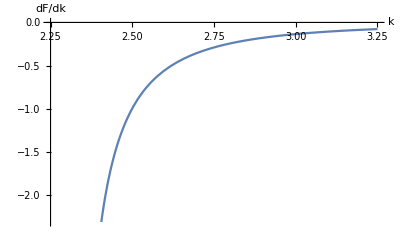

```mathematica
Plot[kderiv[k],{k,datak-0.5,datak+0.5},AxesLabel->{k,dF/dk}]
```

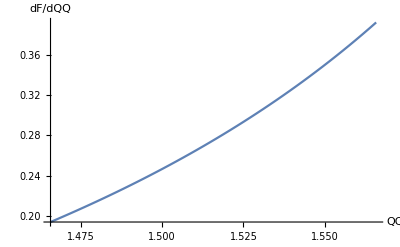

```mathematica
Plot[QQderiv[QQ],{QQ,dataQQ-0.05,dataQQ+0.05},AxesLabel->{QQ,dF/dQQ}]
```

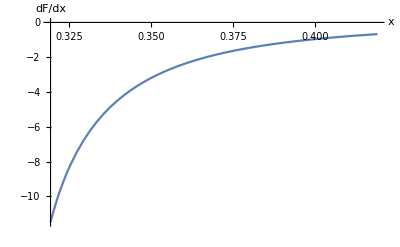

```mathematica
Plot[xderiv[x],{x,datax-0.05,datax+0.05},AxesLabel->{x,dF/dx}]
```

```mathematica
Plot[tderiv[t],{t,datat-0.05,datat+0.05},AxesLabel->{t,dF/dt}]
```

-Graphics-

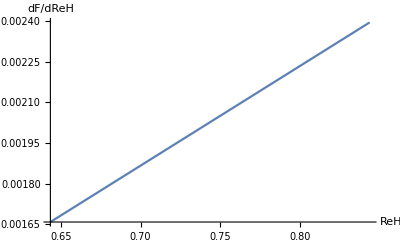

```mathematica
Plot[ReHderiv[ReH],{ReH,dataReH-0.1,dataReH+0.1},AxesLabel->{ReH,dF/dReH}]
```

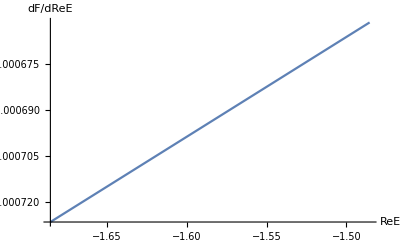

```mathematica
Plot[ReEderiv[ReE],{ReE,dataReE-0.1,dataReE+0.1},AxesLabel->{ReE,dF/dReE}]
```

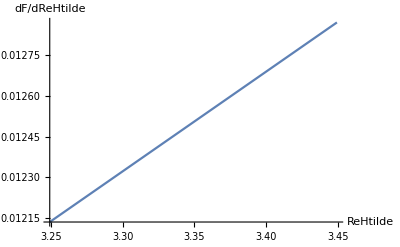

```mathematica
Plot[ReHtildederiv[ReHtilde],{ReHtilde,dataReHtilde-0.1,dataReHtilde+0.1},AxesLabel->{ReHtilde,dF/dReHtilde}]
```

```mathematica
(*Plot3D[kQQderiv[k,QQ],{k,datak-0.5,datak+0.5},{QQ,dataQQ-0.05,dataQQ+0.05},AxesLabel->{k,QQ,d2F/dk dQQ}]*)
```